## Dicke Hamiltonian

```mathematica
(*Constants*)
bsize=16;ω0=1.0; ωc = 1.0; K = 4;
(*Identity matrices for TLS and QHO*)
idTSS=SparseArray[IdentityMatrix[2]];
idHO=SparseArray[IdentityMatrix[bsize]];

(*TLS initial Hamiltonian*)
H0TSS=SparseArray[Band[{1,1}]->{ω0/2,-ω0/2}];
(*QHO Hamiltonian*)
H0HO=ωc * SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*TLS raising and lowering operators*)
σm={{0,0},{1,0}};
σp={{0,1},{0,0}};
σx = σm + σp;

(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; 

(*Function to construct the total Hamiltonian for a given j*)
constructHtot[j_]:=Module[{Htot,leftIds,rightIds,H0TSSi,σxi},

(*Scaled harmonic oscillator Hamiltonian,using convention with TLS on the left*)
Htot=KroneckerProduct[IdentityMatrix[2^K],H0HO];

Do[
(*Tensor product adjustment for the i-th TLS*)
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
(*TLS Hamiltonian for the i-th TLS*)
H0TSSi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,H0TSS],Sequence@@rightIds];
(*Adding ith TLS Hamiltonian to the total Hamiltonian*)
Htot+=KroneckerProduct[H0TSSi,idHO];
σxi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σx],Sequence@@rightIds];
Htot+=j*(KroneckerProduct[σxi,a]+KroneckerProduct[σxi,a†]);
,{i,K}];
Htot
]
```

### Plot Attempts

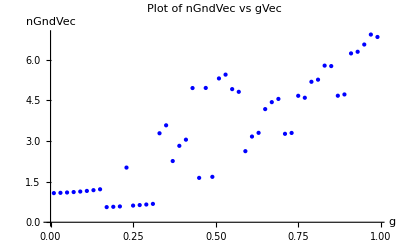

```mathematica
gVec=Table[g,{g,0.01,1.0,0.02}];

psiGndList=Table[Last[Eigensystem[constructHtot[g],-1]] //Flatten,{g,gVec}];

aDaggerA=KroneckerProduct[IdentityMatrix[2^K],a†.a];

(*Cavity ground state occupation probability*)
nGndVec=Table[psi†.aDaggerA.psi,{psi,psiGndList}];
ListPlot[Transpose[{gVec,nGndVec}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"g","nGndVec"},PlotLabel->"Plot of nGndVec vs gVec"]
```